{0.322,-2.12×10^-16,-0.111}

2.114

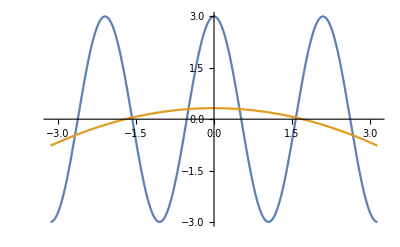

```mathematica
f[x_]:=3Cos[3x];
a=-Pi;
b=Pi;
n=50;
x=Table[0,{i,51},{j,2}];
For[i=1,i≤n+1,i++,x[[i]][[1]]=a+(i-1)*(b-a)/50.;
x[[i]][[2]]=f[x[[i]][[1]]];]
d=Table[0,{i,3},{j,3}];
d[[1]][[1]]=n+1.;
For[i=1,i≤n+1,i++,d[[1]][[2]]+=x[[i]][[1]];];
For[i=1,i≤n+1,i++,d[[1]][[3]]+=x[[i]][[1]]^2;];
d[[2]][[2]]=d[[1]][[3]];
d[[3]][[1]]=d[[1]][[3]];
d[[2]][[1]]=d[[1]][[2]];
For[i=1,i≤n+1,i++,d[[3]][[2]]+=x[[i]][[1]]^3;];
d[[2]][[3]]=d[[3]][[2]];
For[i=1,i≤n+1,i++,d[[3]][[3]]+=x[[i]][[1]]^4;];
y={0,0,0};
For[i=1,i≤n+1,i++,y[[1]]+=x[[i]][[2]];];
For[i=1,i≤n+1,i++,y[[2]]+=x[[i]][[1]]*x[[i]][[2]];];
For[i=1,i≤n+1,i++,y[[3]]+=x[[i]][[1]]^2*x[[i]][[2]];];
q=LinearSolve[d,y];
s[t_]:=q[[1]]+q[[2]]*t+q[[3]]*t^2;
sr_kv=0;
For[i=1, i≤n+1, i++, sr_kv+=(s[x[[i]][[1]]]-x[[i]][[2]])^2;]
Print[NumberForm[q,3]];
Print[Sqrt[sr_kv/(n+1)]];
```